```mathematica
dbticks=Table[{l*10-5,ToString[l*10-5],{0,.005}},{l,1,4}]
fticks2=Table[{l*1000,ToString[l],{0,.005}},{l,1,7}]
```

{{5,5,{0,0.005}},{15,15,{0,0.005}},{25,25,{0,0.005}},{35,35,{0,0.005}}}

{{1000,1,{0,0.005}},{2000,2,{0,0.005}},{3000,3,{0,0.005}},{4000,4,{0,0.005}},{5000,5,{0,0.005}},{6000,6,{0,0.005}},{7000,7,{0,0.005}}}

```mathematica
Plot[{20*Log[10,Abs[SL/S0]]/.θ->90,5*Arg[SL/S0]/(k*L)/.θ->90},{f,100,3500},PlotRange->All,AxesOrigin->{f0,3}]
```

```mathematica
Tokaydiff=20*Log10[Abs[SL/S0]]/.θ->90;
```

```mathematica
Hemidactylusdiff=20*Log10[Abs[SL/S0]]/.θ->90;
```

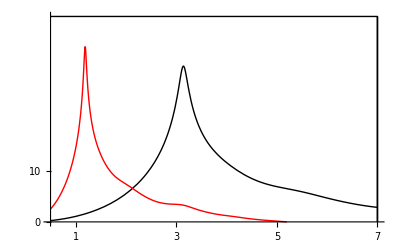

```mathematica
Plot[{Hemidactylusdiff,Tokaydiff},{f,500,7000},PlotRange->{{500,7000.01},{0,40}},PlotStyle->{Black,Red},Ticks->{fticks2,dbticks,None,None},AxesOrigin->{500,0},Epilog->{Line[{{500,40},{7000,40},{7000,0},{7000,40}}]},PlotLegend->{Style["Hemidactylus",Black,18],Style["Tokay",Black,18]},LegendPosition->{1.0,-.3}]
```

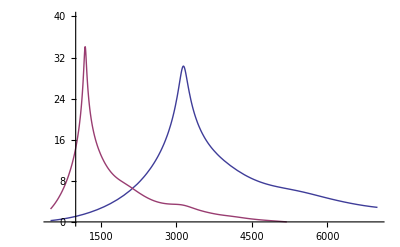

```mathematica
Plot[{Hemidactylusdiff,Tokaydiff},{f,500,7000},PlotRange->{{500,7000.01},{0,40}}]
```

{{0,0,{0,0.005}},{25,25,{0,0.005}},{50,50,{0,0.005}},{75,75,{0,0.005}},{100,100,{0,0.005}},{125,125,{0,0.005}},{150,150,{0,0.005}},{175,175,{0,0.005}},{200,200,{0,0.005}},{225,225,{0,0.005}}}

{{1000,0.5,{0,0.005}},{2000,1.,{0,0.005}},{3000,1.5,{0,0.005}},{4000,2.,{0,0.005}},{5000,2.5,{0,0.005}},{6000,3.,{0,0.005}},{7000,3.5,{0,0.005}}}

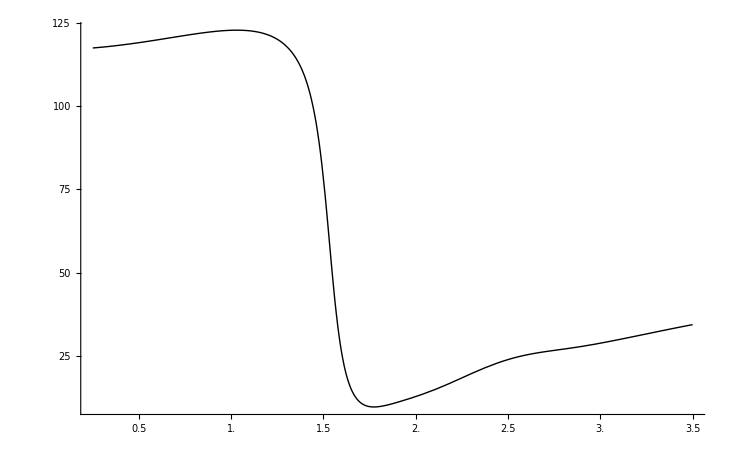

```mathematica
tticks=Table[{l*25-25,ToString[l*25-25],{0,.005}},{l,1,10}]
fticks=Table[{l*1000,ToString[N[l/2]],{0,.005}},{l,1,7}]
Plot[{10^6*Arg[SL/S0]/ω/.θ->90},{f,500,7000},PlotRange->All,AxesOrigin->{500,0},Ticks->{fticks,tticks},PlotRange->All,PlotStyle->Black]
```

{{1000,0.5,{0,0.005}},{2000,1.,{0,0.005}},{3000,1.5,{0,0.005}},{4000,2.,{0,0.005}},{5000,2.5,{0,0.005}},{6000,3.,{0,0.005}},{7000,3.5,{0,0.005}},{8000,4.,{0,0.005}}}

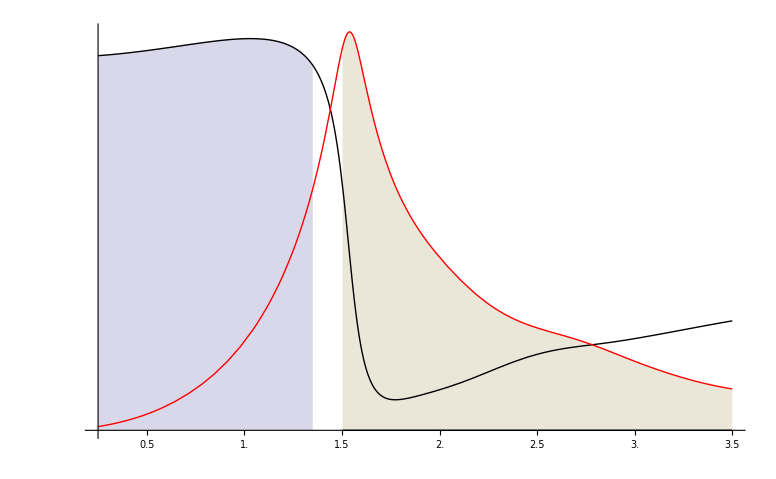

```mathematica
fticks=Table[{l*1000,ToString[N[l/2]],{0,.005}},{l,1,8}]
Plot[{8*Arg[SL/S0]/Arg[pL/p0]/.θ->90,If[500≤f≤2700,0],20*Log10[Abs[SL/S0]]/.θ->90,
If[3005≤f≤7000,0]},{f,500,7000},PlotRange->All,AxesOrigin->{500,0},PlotStyle->{Black,None,Red},Filling->{1->{2},3->{4}},Ticks->{fticks,None}]
```

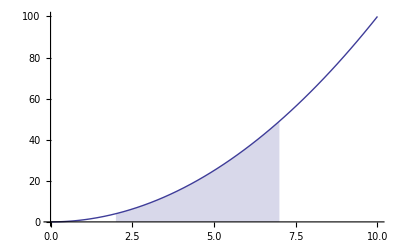

```mathematica
Plot[{x^2,If[2≤x≤7,0]},{x,0,10},PlotStyle->{Automatic,None},Filling->{1->{2}}]
```